7

狄拉克 δ 函数

## 7.1 狄拉克 δ 函数

δ 函数是一种广义函数 generalized function，也称分布 distribution。

现在被认为 1930年由物理学家狄拉克 (Paul Dirac) 在物理上引入。

其实英国工程师赫维赛德 (Heaviside)更早引入之，目前只记得他的阶跃函数 θ(x)，而阶跃函数的导数即 δ 函数

1950 Laurent Schwartz 建立严格的数学理论 —— 广义函数理论。

更多关于广义函数的介绍，可参阅

M. J. Lighthill,  "An Introduction to Fourier Analysis and Generalized Functions " (Cambridge University 1958).

Schwartz：《广义函数论》

陆振球：《经典和现代数学物理方法》第二篇之第四章

本章还是从普通函数的角度理解。从广义函数的角度来理解，可参阅上三本书相关章节。

### δ 函数的物理定义

中心位于 x_0长度为 l 、总电量为 q=1 的均匀带电细线段，电荷的线密度 λ(x) 可写成：

λ(x)=Piecewise[{{0, |x-x_0|>l/2}, {q/l=1/l, |x-x_0|≤ l/2}}]       满足   ∫_(-∞)^∞ λ(x)ⅆx=q=1

现让细线段的长度 l→0，这时的线电荷密度变为

λ(x)=Piecewise[{{0, x-x_0≠0}, {∞, x-x_0=0}}]       仍然满足：∫_(-∞)^∞ λ(x)ⅆx=q=1

因此，将定义在区间 (-∞,+∞) 上，满足上述两条件的函数，称为一维 δ 函数，即：

δ(x-x_0)=Piecewise[{{0, x-x_0≠0}, {∞, x-x_0=0}}]  ，            ∫_(-∞)^∞ δ(x-x_0)ⅆx=1

定义了一维 δ 函数，则带电为  q ，中心位于 x=x_0，长度趋于 0 的细小线段，其线电荷密度 λ(x)=q δ(x-x_0)。

起初，物理上定义 δ 函数的目的仅在于简化对函数的微积分运算。直到发展了广义函数论后，才有严格的数学理论。

因为在数学家眼里，这个 δ 函数过于“病态”，粗鲁的。

物理学家的粗鲁让数学家们娇羞无限，欲拒还迎。

不得不推广函数理论。在十余年之后的1950年，法国数学家 Schwartz 建立了广义函数论。

作为“物理课程”，我们在涉及 δ 函数等式的证明方面，传承物理学家的粗犷，

均通过所谓"物理学家的证明方法"来论证，牺牲了数学上的严谨性。

“物理学家的证明方法”：对于涉及 δ 函数的证明，本节均通过判断下式是否成立来论证。

∫_(-∞)^∞ f(x)D_1(x)ⅆx=∫_(-∞)^∞ f(x)D_2(x)ⅆx     ⟹    D_1(x)=D_2(x)，

其中 f(x)为普通的连续函数，D_1(x)和 D_2(x) 涉及 δ 函数的函数（广义函数）

也就是说，这里说的证明，与其说是证明，不如说是一种理解、说明。

若希望更严谨的数学论证，请参阅 Lighthill 或 陆振球。

不过，实际上通过广义函数理论的证明，也是基于此式：∫_(-∞)^∞ f(x)D_1(x)ⅆx=∫_(-∞)^∞ f(x)D_2(x)ⅆx

只是语言表达与数学处理上有差异，因而，所谓“物理学家的证明方法”，还是可靠的。

例如：函数 f=x^2 作为广义函 数和作为普通点函数是不同的，

在普通函数的意义上，x=0 时，f=0

而在广义函数的意义下：在 x=0，f=x^2≠0

但若局限于普通函数论，用一些在普通函数论中让人欲拒还迎的做法，

得到的结论与广义函数论并不产生矛盾。

即：物理学家那些开始阶段被数学家视为大逆不道的做法，最后也终被新的数学理论所证明。

### δ 函数的性质

如前所述，以下性质仅在普通函数论予以证明（理解），更严谨地，可在广义函数理论中证明。

I=∫_(-∞)^(+∞) f(x)δ(x-x_0)ⅆx=f(x_0),   对任意的连续函数 f(x)，这个性质称为： sifting  property

证明：利用 δ 函数的定义

I=∫_(-∞)^∞ f(x)δ(x-x_0)ⅆx=lim_(ε→0^+) ∫_(x_0-ε)^(x_0+ε) f(x)δ(x-x_0)ⅆx,  其中 ε→0^+表示 ε>0 且 ε→0
=(lim_(ε→0^+) ∫_(x_0-ε)^(x_0+ε) [f(x)-f(x_0)]δ(x-x_0)ⅆx)_(⏟_Δ)+lim_(ε→0^+) ∫_(x_0-ε)^(x_0+ε) f(x_0)δ(x-x_0)ⅆx
=Δ+f(x_0),

|Δ|=|lim_(ε→0^+) ∫_(x_0-ε)^(x_0+ε) [f(x)-f(x_0)]δ(x-x_0)ⅆx |
≤ lim_(ε→0^+) ∫_(x_0-ε)^(x_0+ε) |f(x)-f(x_0)|δ(x-x_0)ⅆx，   连续函数：ε→0 时, |f(x)-f(x_0)|<η
≤ lim_(ε→0^+) η∫_(x_0-ε)^(x_0+ε) δ(x-x_0)ⅆx=lim_(ε→0^+) η=0

∫_(-∞)^(+∞) f(x)δ(x-x_0)ⅆx=f(x_0)   常称为 sifting property

表明 δ 函数可理解为“采样函数”，采集连续函数在 x_0 点的函数值

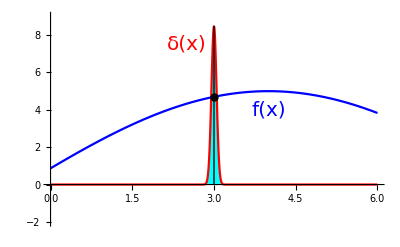

```mathematica
f[n_]:=n/(√π)ⅇ^(-n^2(x-3)^2);
g1=Plot[{f[n0=15],5Sin[((x+0.5) π)/9] },{x,0,6},PlotRange->{-2,9},PlotStyle->{{Red},{Blue}},Ticks->None,Filling->{1->{Axis,Cyan}}];
g2=Graphics[{Line[{{3,0},{3,8.5}}],PointSize[0.015],Point[{3,4.7}],
         Text[Style["f(x)",FontFamily->Times,Blue,Italic,20],{4,4}],
         Text[Style["δ(x)",FontFamily->Times,Red,20],{2.5,7.5}]}];
Show[g1,g2]
```

δ(x-x_0)=δ(x_0-x)

证明：利用涉及 δ 函数的“物理学家的证明方法”，设：左边为 D_1(x)，右边为 D_2(x)

左=∫_(-∞)^∞ f(x)D_1(x)ⅆx=∫_(-∞)^∞ f(x)δ(x-x_0)ⅆx=f(x_0)

右=∫_(-∞)^∞ f(x)D_2(x)ⅆx=∫_(-∞)^∞ f(x)δ(x_0-x)ⅆx

⟹^(令 x_0-x = t)  ∫_∞^(-∞) f(x_0-t)δ(t)ⅆ(-t) =f(x_0)

左=右，故： D_1(x)=D_2(x)，即：δ(x-x_0)=δ(x_0-x)

g(x) δ(x-x_0)=g(x_0) δ(x-x_0)

证明：类似地，设：左边为 D_1(x)，右边为 D_2(x)

∫_(-∞)^∞ f(x)D_1(x)ⅆx=∫_(-∞)^∞ f(x)g(x)δ(x-x_0)ⅆx=f(x_0)g(x_0)

∫_(-∞)^∞ f(x)D_2(x)ⅆx=∫_(-∞)^∞ f(x)g(x_0)δ(x-x_0)ⅆx=f(x_0)g(x_0),   得证。

推论：x δ(x)=0

特别注意：f(x)δ(x)=g(x)δ(x) 不能导出 f(x)=g(x)，因为f(x)δ(x)=f(0)δ(x) ，

f(x)δ(x)=g(x)δ(x)   ⟹  f(0)=g(0)   但不能得到：f(x)=g(x)

若 φ(x) 为连续函数，且 φ(x) 仅有一阶零点 x_k, k=1,2,…,N，则

δ[φ(x)]=(∑_(k=1))^N(δ(x-x_k))/(|φ'(x_k)|)

证明：因为 δ 函数仅在其宗量（自变量）为 0 时才不为 0，故

δ[φ(x)]=(∑_(k=1))^N c_k δ(x-x_k)， x_k 是 φ(x) 的一阶零点

两边同时对 x 从 x_l-ε 到 x_l+ε 积分，取 ε→0^+使得 φ(x) 在积分区间[ x_l-ε, x_l+ε]仅有一个零点 x_l

右=∫_(x_l-ε)^(x_l+ε) (∑_(k=1))^N c_k δ(x-x_k)ⅆx=(∑_(k=1))^N c_k∫_(x_l-ε)^(x_l+ε) δ(x-x_k)ⅆx=c_l

左=∫_(x_l-ε)^(x_l+ε) δ[φ(x)]ⅆx=∫_(x_l-ε)^(x_l+ε) δ[φ(x)](ⅆφ(x))/(φ'(x)),      注意在一阶零点 x_l 邻域，连续函数 φ'(x_l)≠0   ⟹    φ'(x)≠0
=∫_(φ(x_l-ε))^(φ(x_l+ε)) δ(t)ⅆt/(φ'(x))=1/(φ'(ξ))∫_(φ(x_l-ε))^(φ(x_l+ε)) δ(t)ⅆt ,        其中 t=φ(x)，x_l-ε <ξ<x_l+ε
={1/(φ'(ξ))∫_(φ(x_l-ε))^(φ(x_l+ε)) δ(t)ⅆt =1/(φ'(x_l)),     当 φ(x_l+ε)>φ(x_l-ε)即 φ'(x_l)>0 时
1/(φ'(ξ))∫_(φ(x_l-ε))^(φ(x_l+ε)) δ(t)ⅆt =-1/(φ'(x_l)), 当 φ(x_l+ε)<φ(x_l-ε) 即φ'(x_l)<0 时                  
=1/(|φ'(x_l)|)      ⟹     c_l=1/(|φ'(x_l)|)     ⟹     δ[φ(x)]=(∑_(k=1))^N(δ(x-x_k))/(|φ'(x_k)|)

或：   左=∫_(φ(x_l-ε))^(φ(x_l+ε)) δ(t)ⅆt/(φ'(x))=∫_(φ(x_l-ε))^(φ(x_l+ε)) δ(t)g(t)ⅆt，其中 g(t)=1/(φ'(x))=1/φ'[φ^-1(t)]

若  φ'(x) >0,  则：t_2=φ(x_l+ε)>φ(x_l-ε)=t_1,   t_2>0>t_1

左=∫_t_1^t_2 δ(t)g(t)ⅆt=g(0)=1/φ'[φ^-1(0)]=1/φ'[x_l]

若  φ'(x) <0,  则：t_2=φ(x_l+ε)<φ(x_l-ε)=t_1,   t_1>0>t_2

左=∫_t_1^t_2 δ(t)g(t)ⅆt=-∫_t_2^t_1 δ(t)g(t)ⅆt=-g(0)=-1/φ'[x_l]

推论

δ(a x-b)=(δ(x-b/a))/(|a|),   δ(x^2-a^2)=(δ(x+a)+δ(x-a))/(2|a|),      δ(sin x)=(∑_(k=-∞))^∞δ(x-k π)

思考：将 δ(sin x) 写成 Fourier 级数。

### δ 函数的常用极限表达式

δ(x)=lim_(u→∞) (sin^2(x u))/(π x^2 u)=lim_(n→∞) n/(√π)ⅇ^(-n^2 x^2)=lim_(ε→0) ε/(π(x^2+ε^2))=lim_(n→∞) n/(π(n^2 x^2+1))

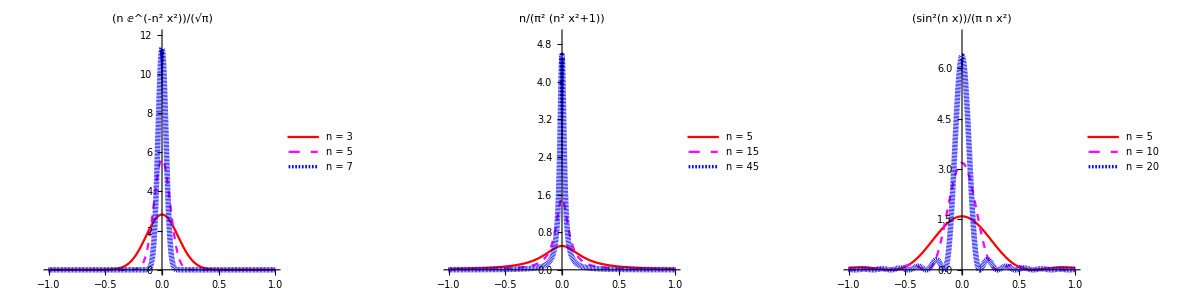

```mathematica
Clear["Global`*"]
f[n_]:=n/(√π)ⅇ^(-n^2 x^2);
g1=Plot[{f[n0=5],f[n0=10],f[n0=20]},{x,-1,1},PlotRange->{0,12},PlotStyle->{{Red},{Magenta,Dashed},{Blue,Thickness[0.01],Dashing[0.00]}},
PlotLabel->f[n],          PlotLegends->Placed[LineLegend[{Style["n = 3",Italic,10],Style["n = 5",Italic,10],Style["n = 7",Italic,10]},LegendMarkerSize->{30,10}],{0.8,0.7}]];
f[n_]:=1/π n/(π(n^2 x^2+1));
g2=Plot[{f[n0=5],f[n0=15],f[n0=45]},{x,-1,1},PlotRange->{0,5},PlotStyle->{{Red},{Magenta,Dashed},{Blue,Thickness[0.01],Dashing[0.0]}},
PlotLabel->f[n],          PlotLegends->Placed[LineLegend[{Style["n = 5",Italic,10],Style["n = 15",Italic,10],Style["n = 45",Italic,10]},LegendMarkerSize->{30,10}],{0.8,0.7}]];
f[n_]:=Sin[x n]^2/(π x^2 n);
g3=Plot[{f[n0=5],f[n0=10],f[n0=20]},{x,-1,1},PlotRange->{0,7},PlotStyle->{{Red},{Magenta,Dashed},{Blue,Thickness[0.01],Dashing[0.0]}},
PlotLabel->f[n],          PlotLegends->Placed[LineLegend[{Style["n = 5",Italic,10],Style["n = 10",Italic,10],Style["n = 20",Italic,10]},LegendMarkerSize->{30,10}],{0.8,0.7}]];
Grid[{{g1,g2,g3}}]
```

选取其中之一加以证明。

lim_(ε→0) ε/(π(x^2+ε^2))={(lim_(ε→0) ε)/(lim_(ε→0) (π x^2+ε^2))=0 |     x≠0
lim_(ε→0) ε/(π ε^2)=∞ | x=0

(⟹        lim_(ε→0) ∫_(-∞)^(+∞) ε/(π(x^2+ε^2))ⅆx=lim_(ε→0) 1/π tg^-1 x/ε|)_(-∞)^(+∞)=1

Heaviside 阶跃函数

Heaviside 在引入阶跃函数时，自然也涉及到 δ 函数，

—— 像一首没有被自己唱红的曲子，反被他人唱红，如汪峰的《春天里》

H(x)=Piecewise[{{0, x<0}, {1, x≥0}}] ，  ⟹      (ⅆH(x))/ⅆx=δ(x)

证明：令 D_1(x)= (ⅆH(x))/ⅆx ，D_2(x)= δ(x)

(∫_(-∞)^(+∞) f(x)D_1(x)ⅆx=∫_(-∞)^(+∞) f(x)(ⅆH(x))/ⅆx ⅆx  ⟹^分部积分  f(x)H(x)|)_(-∞)^(+∞)-∫_(-∞)^(+∞) H(x)f'(x)ⅆx
=f(∞)-∫_0^∞ f'(x)ⅆx=f(∞)-[f(∞)-f(0)]=f(0)

∫_(-∞)^(+∞) f(x)D_2(x)ⅆx=∫_(-∞)^(+∞) f(x)δ(x)ⅆx=f(0)   ⟹   D_1(x)=D_2(x)

### δ 函数的导数

定义：对任何一个在 x=x_0点具有连续导数的函数 f(x)，若

(∫_(-∞)^∞ f(x)δ̃(x-x_0)ⅆx=-(ⅆf(x))/ⅆx|)_(x=x_0)=-f'(x_0)

均成立，则称 δ̃(x-x_0) 为 δ(x-x_0) 的导数。记为：δ̃(x-x_0)=(ⅆ δ(x-x_0))/ⅆx=δ'(x-x_0)

这个定义是利用普通函数的导数运算公式而得，即利用

(∫_(-∞)^∞ f(x)(ⅆ δ(x-x_0))/ⅆx ⅆx  ⟹^分部积分 f(x)δ(x-x_0)|)_(-∞)^∞-∫_(-∞)^∞ δ(x-x_0)f'(x)ⅆx=-f'(x_0)

当然，这只是物理上为运算方便引入。后来数学家用广义函数论给予了严格的数学证明。

类似地，继续利用普通函数的导数运算公式，可以定义 δ 函数的 n 阶导数。即：

对任何一个在 x=x_0点具有连续导数的函数 f(x)，若

(∫_(-∞)^∞ f(x)δ^(n)(x-x_0)ⅆx=(-1)^n(ⅆ^n f(x))/(ⅆ x^n)|)_(x=x_0)=(-1)^n f^(n)(x_0)

成立，则   δ^(n)(x-x_0)=(ⅆ^n δ(x-x_0))/(ⅆ x^n) 为 δ(x-x_0) 的 n 阶导数。

δ 函数导数的性质

δ'(x_0-x)=-δ'(x-x_0)，利用“物理学家的证明方法”，易证

(∫_(-∞)^∞ f(x)δ'(x_0-x)ⅆx =-∫_(-∞)^∞ f(x)ⅆδ(x_0-x)  (⟹^分部积分)^-f(x)δ(x-x_0)|)_(-∞)^(+∞)+∫_(-∞)^∞ δ(x_0-x)f'(x)ⅆx=f'(x_0)

理解：因为 δ(x)=δ(-x)   ⟹   δ(x)为 “偶函数”   ⟹   δ'(x) 为“奇函数”   ⟹    δ'(x)=-δ'(-x)

(x-x_0)δ'(x-x_0)=-δ(x-x_0)，利用“物理学家的证明方法”，易证

∫_(-∞)^∞ f(x)(x-x_0)δ'(x-x_0)ⅆx =-∫_(-∞)^∞ (x-x_0)f(x)ⅆδ(x-x_0)  ⟹^分部积分∫_(-∞)^∞ δ(x-x_0)[(x-x_0)f(x)]' ⅆx=f'(x_0)

### 三维 δ 函数

对三维空间，相应地，在不同坐标系下，三维 δ 函数定义为：

δ(r⃗-r⃗')={δ(x-x')δ(y-y')δ(z-z')                        直角坐标系
1/(r^2 sin θ)δ(r-r')δ(θ-θ')δ(ϕ-ϕ')        球坐标系
1/ρ δ(ρ-ρ')δ(ϕ-ϕ')δ(z-z')                  柱坐标系

其中利用了在三个坐标系下小体积元的表达式： ⅆτ=ⅆxⅆyⅆz=r^2 sin θ ⅆrⅆθⅆϕ=ρ ⅆρⅆϕⅆz

∫_(V_∞) δ(r⃗-(a⃗)^)ⅆτ=1，     ∫_(V_∞) f(r⃗)δ(r⃗-(a⃗)^)ⅆτ=f(a⃗)

在三维空间，一个位于  r⃗=a⃗  的点电荷 q，其电荷密度表为： ρ_q(r⃗)=q δ(r⃗-a⃗)

### 例题

例 1：求位于 r⃗=a⃗ 点电偶极子的电荷密度 ρ_p(r⃗)

解：对位于 a⃗ 处的点电荷，电荷密度可表为： ρ_q(r⃗)=q δ(r⃗-a⃗)

电偶极子由相距很近的一对点电荷构成。

设电偶极子的两个点电荷-q 与+q 分别位于  r⃗=a⃗ 与  r⃗=a⃗+l⃗

电偶极矩  p⃗=lim_(q→∞
l → 0) q l⃗   并且：lim_(q→∞
l → 0) q × ( l⃗ 的高阶项)=0

把电荷密度表为两点电荷之和：ρ_p(r⃗)=q [δ(r⃗-a⃗-l⃗)-δ(r⃗-a⃗)]

对 δ(r⃗-a⃗-l⃗) 做 Taylor 展开：

f(r⃗-a⃗-l⃗)=f(r⃗-a⃗)+(-l⃗)·∇f(r⃗-a⃗)+( l⃗ 的高阶项)

即：δ(r⃗-a⃗-l⃗)=δ(r⃗-a⃗)+(-l⃗)·∇δ(r⃗-a⃗)+( l⃗ 的高阶项),

这一步似乎相当野蛮，一个不连续的函数，居然做 Taylor 展开。

但基于广义函数理论，却是正确的，只不过不称为Taylor 展开而已。

代入 ρ_p(r⃗) 的表达式得：ρ_p(r⃗)=q(-l⃗)·∇δ(r⃗-a⃗)+q × ( l⃗ 的高阶项)

取极限 {q→∞
l→0：    ρ_p(r⃗)=lim_(q→∞
l → 0) q(-l⃗)·∇δ(r⃗-a⃗)+(lim_(q→∞
l → 0) q × ( l⃗ 的高阶项))^(⏞^(此极限为 0))=-p⃗·∇δ(r⃗-a⃗)

从而，一个位于  r⃗=a⃗ 的点电偶极子，其电荷密度：

ρ_p(r⃗)=-p⃗·∇δ(r⃗-a⃗)

例 2：求对应于：∫f(x)δ'(x-x_0)ⅆx=-f'(x_0) 的三维形式。

一维：∫_(-∞)^∞ δ(x-a)ⅆx=1，∫_(-∞)^∞ f(x)δ(x-a)ⅆx=f(a)

三维：∫_(V_∞) δ(r⃗-a⃗)ⅆτ=1，∫_(V_∞) f(r⃗)δ(r⃗-a⃗)ⅆτ=f(a⃗)

其导数形式：∫f(x)δ'(x-x_0)ⅆx=-f'(x_0)  对应的三维形式如何？

三维标量函数的“导数”可能是梯度矢量：∇δ(r⃗-a⃗)，矢量函数可同另一个矢量函数至少构成两种不同的乘积

标量积：I_1=∫_(V_∞) g⃗(r⃗)·∇δ(r⃗-a⃗)ⅆτ=∫_(V_∞) ∇·[g⃗(r⃗)δ(r⃗-a⃗)] ⅆτ-∫_(V_∞) [∇·g⃗(r⃗)]δ(r⃗-a⃗) }ⅆτ
=(∮_(S_∞) n⃗·g⃗(r⃗)δ(r⃗-a⃗)ⅆσ)_(⏟_(在表面，δ(r⃗-a⃗)=0，积分为 0))-∫_(V_∞) [∇·g⃗(r⃗)]δ(r⃗-a⃗) ⅆτ，利用了散度定理：∫_V ∇·A⃗ⅆτ=∮_S n⃗·A⃗ⅆσ
=-[∇·g⃗(r⃗)]|_(r⃗=a⃗)

矢量积：I_2=∫_(V_∞) g⃗(r⃗)×∇δ(r⃗-a⃗)ⅆτ=-∫_(V_∞) ∇×[g⃗(r⃗)δ(r⃗-a⃗)]ⅆτ+∫_(V_∞) [∇×g⃗(r⃗)]δ(r⃗-a⃗) ⅆτ
=(-∮_(S_∞) n⃗ × g⃗(r⃗)δ(r⃗-a⃗)ⅆσ)_(⏟_(在表面，δ(r⃗-(a⃗)^)=0，积分为 0))+∫_(V_∞) [∇×g⃗(r⃗)]δ(r⃗-a⃗) ⅆτ，利用了旋度定理：∫_V ∇×A⃗ⅆτ=∮_S n⃗×A⃗ⅆσ
=[∇×g⃗(r⃗)]|_(r⃗=a⃗)

当然，也可以与标量函数构成乘积：

I_3=∫_(V_∞) f(r⃗)∇δ(r⃗-a⃗)ⅆτ=∫_(V_∞) ∇[f(r⃗)δ(r⃗-a⃗)]ⅆτ-∫_(V_∞) [∇f(r⃗)]δ(r⃗-a⃗) ⅆτ
=(∮_(S_∞) n⃗ [f(r⃗)δ(r⃗-a⃗)]ⅆσ)_(⏟_(在表面，δ(r⃗-(a⃗)^)=0，积分为 0))-∫_(V_∞) [∇f(r⃗)]δ(r⃗-a⃗) ⅆτ，利用了梯度定理：∫_V (∇A)ⅆτ=∮_S (n⃗ A)ⅆσ
(=-[∇f(r⃗)]|)_(r⃗=a⃗)

偶极矩

∫_(V_∞) ρ_p(r⃗)r⃗ ⅆτ=∫_(V_∞) [-p⃗·∇δ(r⃗-a⃗)]r⃗ ⅆτ=-∫_(V_∞) { [∇δ(r⃗-a⃗)]·p⃗ } r⃗ ⅆτ
(=-∫_(V_∞) { [∇δ(r⃗-a⃗)]·(p⃗ r⃗)ⅆτ = [∇·(p⃗ r⃗)]|)_(r⃗=a⃗)=p⃗

其中：∇·(p⃗ r⃗)=(p⃗·∇) r⃗=p⃗·(∇r⃗)=p⃗·Î=p⃗,    Î 为单位张量

例 3： 求  ∇· (r⃗)/r^3

解：∇=x̂ ∂/(∂x)+ŷ ∂/(∂y)+ẑ ∂/(∂z),     x̂, ŷ, ẑ 为沿直角坐标三个单位向量

r⃗= x x̂ +y ŷ +z ẑ,      常称为位置矢量，r=√(x^2+y^2+z^2)

r≠0时

∇· (r⃗)/r^3=(x̂ ∂/(∂x)+ŷ ∂/(∂y)+ẑ ∂/(∂z))·(x x̂ +y ŷ +z ẑ)/((x^2+y^2+z^2)^(3/2))
= ∂/(∂x)[x/((x^2+y^2+z^2)^(3/2))] +∂/(∂y)[y/((x^2+y^2+z^2)^(3/2))] +∂/(∂z)[z/((x^2+y^2+z^2)^(3/2))]

∂/(∂x)[x/((x^2+y^2+z^2)^(3/2))]=1/((x^2+y^2+z^2)^(3/2))-(3 x^2)/((x^2+y^2+z^2)^(5/2))

故：∇· (r⃗)/r^3=3/((x^2+y^2+z^2)^(3/2))-(3(x^2+y^2+z^2))/((x^2+y^2+z^2)^(5/2))=0

r=0时：(r⃗)/r^3 发散，显然不能直接求偏导

从散度的定义出发：

∫_V [∇· (r⃗)/r^3]ⅆτ=∮_S [n⃗· (r⃗)/r^3]ⅆσ     其中 V 为半径为 a 的小球，S 为其球面
=∮_S [n⃗· (a n⃗)/a^3]a^2 ⅆΩ     其中 n⃗ 为 S 球面外法线方向，ⅆΩ 为立体角元
=4π
=4π ∫_V δ(r⃗)ⅆτ            注意到 ∇· (r⃗)/r^3=0  if    r⃗≠0

从而：∇· (r⃗)/r^3=4π δ(r⃗)

例 4： 再来品味一下物理学家的粗狂（这里仅仅用于理解，不构成数学“证明”）

在复变函数中，知   (ⅆln z)/ⅆz=1/z

故：    (ⅆln (x+ⅈ ε))/ⅆx=1/(x+ⅈ ε) 
另一方面：
         ln (x+ⅈ ε)=ln|x+ⅈ ε|+ⅈ arg (x+ⅈ ε)
现令 ε→0^+  （0^+表示从大于 0 趋于 0）
  右图显示
                 x>0 时，lim_(ε→0^+) arg (x+ⅈ ε)=0
x<0 时，lim_(ε→0^+) arg (x+ⅈ ε)=π
 从而：      
    lim_(ε→0^+) ln (x+ⅈ ε)= lim_(ε→0^+) ln|x+ⅈ ε|+ⅈ π [1-θ(x)] 
                                       = ln |x|+ⅈ π [1-θ(x)]       -Graphics-

这里      θ(x) 为 Heaviside 阶跃函数

所以有：lim_(ε→0^+) ln (x+ⅈ ε)=  ln |x|+ⅈ π [1-θ(x)]

两边同时对 x 求导：   左=  lim_(ε→0^+) (ⅆln (x+ⅈ ε))/ⅆx=lim_(ε→0^+) 1/(x+ⅈ ε)

右 = (ⅆ ln|x|)/ⅆx-ⅈ π δ(x)       其中：(ⅆθ(x))/ⅆx=δ(x)

记得：(ⅆ ln|x|)/ⅆx=𝒫/x               𝒫 表示 Cauchy 主值

⟹    1/(x+ⅈ 0^+)=𝒫/x -ⅈ π δ(x)              类似可得：  1/(x-ⅈ 0^+)=𝒫/x +ⅈ π δ(x)

即：  1^/(x_±ⅈ 0^+)=𝒫/x∓ ⅈ π δ(x)        ——  Dirac-Plemelj 关系

我们将在 Fourier 变换一章再做更细致的证明。

(ⅆ ln|x|)/ⅆx=𝒫/x 的理解：仅在积分时显现，广义函数也是在此意义上定义的

(∫_-a^b (ⅆ ln|x|)/ⅆx ⅆx=∫_-a^b ⅆ ln|x|=(ln |x|)|)_-a^b=ln|b/a|         其中 a, b >0

∫_-a^b  𝒫/x ⅆx=∫_-a^-ϵ  1/x ⅆx+∫_ϵ^a  1/x ⅆx+∫_a^b  1/x ⅆx    注意两 ϵ 相同
=(∫_a^ϵ 1/t ⅆt+∫_ϵ^a  1/x ⅆx)_(⏟_(主值积分， ϵ 相同，两项相消))+ln b/a=ln b/a

```mathematica
Integrate[1/x,{x,-3,2}]
Integrate[1/x,{x,-3,2}, PrincipalValue->True]
```

Integrate::idiv: Integral of 1/x does not converge on {-3,2}.

∫_-3^2 1/x ⅆx

-Log[3/2]